# Correction Procedure via Reconstruction (CPR)

## CPR: Flux Reconstruction (FR) / Lifting Collocation Penalty (LCP)

## Coded by Manuel Diaz, NTU, 2013.08.20

Based on Ideas of jounal papers:

1. Z.J. Wang & Hai-Yang Gao, JCP 228 (2009) 8161-8186. -> (LCP)
2. H.T. Huynh, AIAA (2007) 4079.->  (FR)
3. Jie Du, Chi-Wang Shu, MengPing Zhang, Brown University (2013) 15.  -> (CPR)

Derivation of the Method in one-dimensional space.

```mathematica
Quit[]; (* to reset Mathematica kernel *)
```

## Initialize Symbols & Notation

#### Change Notebook BackGround

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[0.1,0.1,0.1]]
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[170/255,240/255,140/255]]
```

#### Adding Notation

```mathematica
Needs["Notation`"]
```

```mathematica
(* Derivatives *)
```

```mathematica
Notation[(∂f_[x_])/(∂x_) ⟸ Derivative[1][f_][x_]]
Notation[(∂^n_ f_[x_])/(∂x_^n_) ⟸ Derivative[n_][f_][x_]]
Notation[(∂f_[x_,y_])/(∂x_) ⟸ Derivative[{1,0}][f_][{x_,y_}]]
Notation[(∂f_[x_,y_])/(∂y_) ⟸ Derivative[{0,1}][f_][{x_,y_}]]
Notation[(∂f_[x_,y_,z_])/(∂x_) ⟸ Derivative[{1,0,0}][f_][{x_,y_,z_}]]
Notation[(∂f_[x_,y_,z_])/(∂y_) ⟸ Derivative[{0,1,0}][f_][{x_,y_,z_}]]
Notation[(∂f_[x_,y_,z_])/(∂z_) ⟸ Derivative[{0,0,1}][f_][{x_,y_,z_}]]
Notation[(∂f_[x_,y_,z_,t_])/(∂x_) ⟸ Derivative[{1,0,0,0}][f_][{x_,y_,z_,t_}]]
Notation[(∂f_[x_,y_,z_,t_])/(∂y_) ⟸ Derivative[{0,1,0,0}][f_][{x_,y_,z_,t_}]]
Notation[(∂f_[x_,y_,z_,t_])/(∂z_) ⟸ Derivative[{0,0,1,0}][f_][{x_,y_,z_,t_}]]
Notation[(∂f_[x_,y_,z_,t_])/(∂t_) ⟸ Derivative[{0,0,0,1}][f_][{x_,y_,z_,t_}]]
```

```mathematica
(* Divergence *)
```

```mathematica
Notation[∇_x_ ·f_ ⟹ Div[{f_[{x_,t}]},{x_}]]
Notation[∇_(x_,y_) ·{f_,g_} ⟹ Div[{f_[{x_,y_,t}],g_[{x_,y_,t}]},{x_,y_}]]
Notation[∇_(x_,y_,z_) ·{f_,g_,h_} ⟹ Div[{f_[{x_,y_,z_,t}],g_[{x_,y_,z_,t}],h_[{x_,y_,z_,t}]},{x_,y_,z_}]]
```

```mathematica
(* For Gauss Rule *)
```

```mathematica
Notation[∫∂_x_ (a_[{x_,t}]b_[x_])ⅆx_ ⟹ a_^(\[MathematicaIcon])[{Subscript[x_, k+1/2],t}] b_[Subscript[x_, k+1/2]] - a_^(\[MathematicaIcon])[{Subscript[x_, k-1/2],t}] b_[Subscript[x_, k-1/2]]]
```

```mathematica
Symbolize[Subscript[f̂, j-1/2]];
```

```mathematica
Symbolize[Subscript[f̂, j+1/2]];
```

```mathematica
Notation[<a_,b_> ⟹ Integrate[a_ b_,{ξ,-1,1}]];
Notation[<<a_,b_>> ⟹ Integrate[a_ b_,{ξ,-1,1}],{}];
```

## Lifting Penaly Collocation Formulation for L4

Let’s assume we are using 4 Lobatto points as our solution points in every element, e.i.,

```mathematica
abscissas = {-1,-1/(√5),1/(√5),1};
weights={1/6,5/6,5/6,1/6};
```

```mathematica
{Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3],Subscript[ξ, 4]}=abscissas; (* also the local coordinates inside Subscript[I, j] *)
{Subscript[w, 1],Subscript[w, 2],Subscript[w, 3],Subscript[w, 4]}=weights;
```

with state values,

```mathematica
StencilPoints[r_] := Table[{Subscript[ξ, i],Subscript[q, i]},{i,1,r}]
```

```mathematica
StencilPoints[4]
```

{{-1,q_1},{-1/(√5),q_2},{1/(√5),q_3},{1,q_4}}

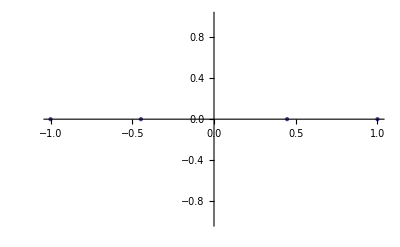

```mathematica
ListPlot[{{-1,0},{-1/(√5),0},{1/(√5),0},{1,0}},PlotStyle-> PointSize[Large]]
```

Let’s now build a lagrange interpolating function,

```mathematica
LagrangePolynomials[r_] := Collect[InterpolatingPolynomial[StencilPoints[r],ξ],u,Simplify]
```

```mathematica
Subscript[q, j][ξ_]:=Evaluate[LagrangePolynomials[4]]
```

```mathematica
Subscript[q, j][0]
```

1/8 (-q_1+5 q_2+5 q_3-q_4)

ok, but this is the final interpolation result, I need to have every lagrange term indepndently, thus:

```mathematica
LagrangePolynomial[data_,x_]/;MatrixQ[data]:=
Module[{n=Length[data], xl,yl},
{xl,yl}=Transpose[data];
Table[Product[(x-xl[[i]])/(xl[[j]]-xl[[i]]),{i,Complement[Range[n],{j}]}],{j,n}]
]
```

```mathematica
{Subscript[ϕ, 1],Subscript[ϕ, 2],Subscript[ϕ, 3],Subscript[ϕ, 4]}=LagrangePolynomial[StencilPoints[4],ξ]//Expand// Simplify
```

{1/8 (-1+ξ+5 ξ^2-5 ξ^3),5/8 (-1+√5 ξ) (-1+ξ^2),-5/8 (1+√5 ξ) (-1+ξ^2),1/8 (-1-ξ+5 ξ^2+5 ξ^3)}

```mathematica
{Subscript[ϕ, 1],Subscript[ϕ, 2],Subscript[ϕ, 3],Subscript[ϕ, 4]}/. ξ->0
```

{-1/8,5/8,5/8,-1/8}

```mathematica
Total[{Subscript[ϕ, 1],Subscript[ϕ, 2],Subscript[ϕ, 3],Subscript[ϕ, 4]}]//Simplify
```

1

Assume I have a way to define,

```mathematica
{Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4]} ;(* my q vector on every SP *)
{Subscript[f, 1],Subscript[f, 2],Subscript[f, 3],Subscript[f, 4]} ;(* my fluxes values on every SP *)
```

Becuase of the Discontinuoity across element interfaces, a common Riemann Flux, f̂, (like lax-friedrichs numerical flux spliting) has been used to replace the normal flux to provide element coupling, i.e.,

```mathematica
Subscript[F, 1] = Subscript[f̂, j+1/2]-Subscript[f, 1]
Subscript[F, 4] = Subscript[f̂, j-1/2]-Subscript[f, 4]
```

(f̂)_(j+1/2)-f_1

(f̂)_(j-1/2)-f_4

### By Flux Reconstruction

As I did before all I need to do if I follow the flux Reconstruction procedure is evaluate:

F_j[ξ_k] = f_j[ξ_k]+((f̂)_(j-1/2)-f_j[-1])ℊ_LB[ξ_k]+((f̂)_(j+1/2)-f_j[1])ℊ_RB[ξ_k]

and substitute it

(∂q_(j,k))/(∂t)+2/h_j(F_j)_ξ[ξ_k]

### The correction Field δ_i ∈ P^k

However if we use the CLP procedure we must compute the “correction field”, δ_i.

Introduce the correction field

∫_v_i W δ_iⅆV = ∫_(∂V_i) W [OverTilde[F]]ⅆS

where 
OverTilde[[F]] = F̃(Q^h, (Q_+)^h,n⃗)-F^n(Q_i^h)

doing w = 1 LCP correction term yields,

∫_V_i δ_i ⅆV == ∫_(∂V_i) [F̃] ⅆS

or

OverBar[δ_i]= 1/(|V_i|)∑_(f∈∂V_i) ∫_f [F̃]ⅆS

using a suitable on the face of every element yields,

OverBar[δ_i]= 1/(|V_i|)∑_(f∈∂V_i) ∑_l w_l[F̃]_(f,l)S_f

For the Linear case, we only have one flux-node at each end of every element, therefore the internal sumation simplifies to.

OverBar[δ_i]= 1/(|V_i|)(∑^2)_f w[F̃]_f S_f

assuming S_fto be unity for linear case is easy to realize that,

OverBar[δ_i]= 1/(|V_i|)(w[F̃]_1+w[F̃]_2)

Therefore if we compare the flux reconstruction with LCP procedure we notice that g(x) is directly related to w in this last equation.